```mathematica
Lecture 9: Single Variable Calculus
```

Key calculus functions include:

```mathematica
{Limit,D,Integrate,NIntegrate,Simplify,FindInstance,Reduce,FindRoot,Solve,Series,Normal,Maximize,NMaximize,Evaluate, ArcLength}
```

Problem ideas: tangent lines to parametric equations, tangent lines to polar equations

## Limits

### Exercise Subsection

Use known Calculus theorems and definitions to predict the output of the following cells:

```mathematica
Clear[f,x,a,c]
Limit[(f[x+h]-f[x])/h,h->0,Analytic->True]
```

```mathematica
Limit[(f[x]-f[a])/(x-a),x->a,Analytic->True]
```

```mathematica
Limit[c f[x],x->a,Analytic->True]==c Limit[f[x],x->a,Analytic->True]
```

### Exercise Subsection

Find the limit of the ratio of consecutive Fibonacci numbers.

### Exercise Subsection

A sequence a[n]where n is a positive integer is defined in the next cell.

```mathematica
a[n_]:=n! ⅇ^n n^(-n-1/2)
```

Create a graphic that shows the ListPlot to plot the first 1000 values of this sequence along with a line depicting its limit at Infinity.

### Exercise Subsection

Plot the function defined in the next cell and then create a graphic showing the plot of the function together with its limit at Infinity.

```mathematica
f[x_]:=(ⅇ^x x+Sin[x]+Cos[x] Sinh[x])/(ⅇ^x x+Sin[x])
```

### Exercise Subsection

a. Produce a graphic that shows the ParametricPlot of the circle described by the parametric equations {Cos[t],Sin[t]} together with the inscribed polygon created by connecting 12 equally spaced points on the circle.

b. Use ArcLength to find the arc length of the inscribed polygon, thereby approximating the value of 2 Pi.

## Derivatives

### Exercise Subsection

Define a function PlotTangentLine[f_, a_] that has input a differentiable function f of one variable and real number a and output the plot of f together with the line tangent to f at a on the interval from a-1 to a+1.

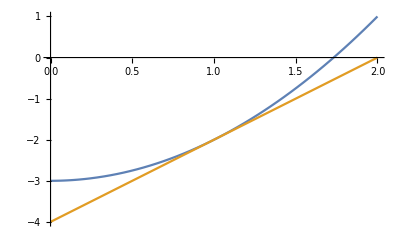

```mathematica
PlotTangentLine[f_,a_]:=Plot[{f[x],(x-a) f'[a] + f[a]},{x,a-1,a+1}]
g[x_]:=x^2-3
PlotTangentLine[g,1]
```

### Exercise Subsection

Find the maximum value of the function x^(a/x) where both x and a are positive.

### Exercise Subsection

The mean value theorem says that if f[x] is differentiable for values of x between a and b, then there a point c strictly between a and b such that f’[c]=(f[b]-f[a])/(b-a).

a. Let f[x] be the function defined in the next cell.  Find one such value of c in the mean value theorem (consider selecting one of the the real elements of NSolve that is in the correct interval) when taking a to be the number that minimizes f[x] (consider Minimize) and b is the number that maximizes f[x] (consider Maximize).

```mathematica
f[x_]:=(x+1)/(2+x^2)
```

b. Plot the following on the same graphic to illustrate the geometric meaning of the mean value theorem. 
1. The Plot of f[x] on the interval from a to b.
2. A Point at each of {a,f[a]}, {b,f[b]}, {c,f[c]}.
3. The InfiniteLine passing through the points {a,f[a]} and {b,f[b]}.
4. The InfiniteLine tangent to f[x] at x=c.

### Exercise Subsection

Newton’s method is an iterative method to find the root of a function f[x].  The idea is to define a recursion x[n] such that x[0] is some initial guess and then x[n] is taken to be the numerical result (take N) of the quantity x[n-1] - f[x[n-1]]/f’[x[n-1]].  Geometrically, Newton’s method approximates the function f[x] with its tangent line at each iteration, and then finds the root of this tangent line.

a. Define the sequence x[n] with initial guess 0 as described by Newton’s method where f[x] is the function defined in the next cell.

```mathematica
f[x_]:=10 Cos[x]-x
```

b. Show a graphic containing the Plot of f[x] together with the sequence of points of the form {x[n], f[x[n]]} for the first 30 values of n, showing convergence to the root .

c. Redo parts a. and b. of this exercise after change the initial guess from 0 to another number of your choosing.

## Integrals

### Exercise Subsection

Use known Calculus theorems and definitions to predict the output of the following cells:

```mathematica
D[∫_a^t f[x]ⅆx,t]
```

```mathematica
∫D[f[x],x]ⅆx
```

### Exercise Subsection

Let f[x_,σ_,μ_] be the function defined in the next cell:

```mathematica
f[x_,σ_/;σ>0,μ_]:=1/(σ √(2 π))Exp[-(x-μ)^2/(2 σ^2)]
```

a. Use Manipulate to Plot the function f as a function of x where σ can take values between 1/4 and 4 and μ values between -4 and 4. Be sure to set PlotRange and any other Plot options to best illustrate the situation.

b. Find all critical points (where the derivative is equal to 0) and all inflection points (where the second derivative is 0) for f as a function of x.  Consider using Reduce as an alternative to Solve.

c. Simplify the Integral of f with respect to x on the interval from 0 to ∞, both without any assumptions and then with the Simplify assumptions of And[Element[σ,Reals],σ >0,μ==0].

### Exercise Subsection

The probabilist's Hermite polynomials are a sequence of polynomials defined by the recursion H[0,x] is equal to 1 and H[n,x] is equal to x H[n-1,x] - D[H[n-1,x],x] otherwise.

a. What is the 50th Hermite polynomial?  (Use Expand in the definition of the recursion together with memoization to get better results.)

b. Create a 8x8 matrix with i,j entry equal to ∫_(-∞)^∞ 1/(√(2 π))Exp[-x^2/2]*H[i,x]*H[j,x]ⅆx and then make a conjecture about what the entries of the corresponding nxn matrix would be.

### Exercise Subsection

The this integral is from the final round of the 2023 MIT integration bee:

```mathematica
Integrate[Tan[x]^(1/3)/(Cos[x]+Sin[x])^2,x]
```

Evaluate the integral and then use FunctionSingularities to describe the values of x for which the resulting function is not defined (where the function has a division by 0 singularity).

### Exercise Subsection

The this integral is from the final round of the 2023 MIT integration bee:

```mathematica
Simplify[Integrate[√(1+x^2+√(1+x^2+x^4)),{x,0,t}],Element[t,Reals]]
```

a. Place the above command in an Simplify command with the assumption Element[t,Reals] to evaluate the above integral.

b. Use FindRoot on the result from part a. to find the first value of t for which the integral Integrate[√(1+x^2+√(1+x^2+x^4)),{x,0,t}] is equal to 1.  Then Plot the function √(1+x^2+√(1+x^2+x^4)) on this interval, using the Filling->Axis option to illustrate the area under the curve that is equal to 1.

### Exercise Subsection

The average value of a function f[x] on the interval from a to b is given by Integrate[f[x],{x,a,b}]/(b-a).  Find a value of t such that the average value of the function Exp[-x] Sin[x] on the interval from 0 to t is equal to 1 (consider FindRoot).

### Exercise Subsection

a. The polar curve described by r as a function of the angle θ is a special case of the parametric equations of the form {r[θ] Cos[θ], r[θ] Sin[θ]}.  Use a Manipulate expression on the ParametricPlot of the polar curve described by the function in the next cell where θ can vary from 0 to 2π where the constant a ranges from 0 to 10.

```mathematica
r[θ_,a_]:=1+a Cos[a θ]
```

b. Use ArcLength to find the arclength of the parametric equations described by the polar curve r[θ,1] where θ can range from 0 to 2π.

c. The area enclosed by a polar curve described by r[θ] as θ ranges between the angles of α and β is given by ∫_α^β r[θ]^2/2 ⅆθ.  Find the area enclosed by the polar equation described by r[θ,a] as defined in part a as θ ranges from 0 to 2 π.  Then find a value of a for which this area is equal to π (consider FindRoot).

### Exercise Subsection

Simpson’s rule approximates the integral of the function f[x] on the interval between a and b with the sum of the form

(b-a)/(3 n)(f[a]+4f[a+(b-a)/n]+2f[a+2(b-a)/n]+4f[a+3(b-a)/n]+...+2f[a+(n-2)(b-a)/n]+4f[a+(n-1)(b-a)/n]+f[b])

where n is an even number and the pattern of coefficients in the sum is 1,4,2,4,2,4,2,4,2,...,2,4,1. 

Let f[x] be the function defined in the next cell.  What is the first even number n such that Simpson’s rule is within .000001 of the true value of the integral of f[x] on the interval from -10 to 10?

```mathematica
f[x_]:=x^5-x Sin[ArcTan[x]+x]
```

## Series

### Exercise Subsection

a. Use ListAnimate to show the Plot of of the function 1/(1-x) on the interval from -4 to 4 together with the degree n polynomial Series[1/(1-x),{x,0,n}] as n ranges from 0 to 25.

b. Redo part a. two more times, once when taking -1 as the center of the series instead of 0, and once when taking 1/2 as the center of the series.

### Exercise Subsection

Use SumConvergence to determine the values of x for which these sum converge:

```mathematica
∑_(n=0)^∞ Log[Log[n]]^-x/(n Log[n])
```

```mathematica
1/2+1/3+1/5+1/7+1/11+1/13+1/17+...
```

```mathematica
∑_(n=1)^∞ x^n/Fibonacci[n]
```

```mathematica
∑_(n=1)^∞ ((-4+x)^n Log[n])/HarmonicNumber[n]
```

### Exercise Subsection

A twin prime is a prime p such that either p-2 or p+2 is also prime.  It is known that the sum of terms of the form 1/p where p is a twin prime converges.  Approximate this sum by selecting the twin primes from the first 10^6 primes and summing the reciprocals.

### Exercise Subsection

Show that the first 100 terms in the series for Exp[I x] is equal to the first 100 terms in the series for Cos[x] + I Sin[x].

```mathematica
Clear[f]
```

```mathematica
Series[Exp[-1/x^2],{x,1,5}]
```

1/ⅇ+(2 (x-1))/ⅇ-(x-1)^2/ⅇ-(2 (x-1)^3)/(3 ⅇ)+(13 (x-1)^4)/(6 ⅇ)-(41 (x-1)^5)/(15 ⅇ)+O[x-1]^6

### Exercise Subsection

The function ChebyshevT[n,x] is a built in function in Mathematica that gives a sequence of polynomials known as the Chebyshev polynomials of the first kind.  

a. Create a list of ChebyshevT[n,x] where n is an integer that ranges from 0 to 10.  Then Plot all of the the polynomials on this list on the interval from -1 to 1.

b. Use CoefficientList to show that the coefficient of t^n in the series centered at t=0 for the function (1-t x)/(1-2 t x + t^2) is equal to ChebyshevT[n,x] for n ranging from 0 to 10.

c. Use CoefficientList to show that the coefficient of t^n in the series centered at t=0 for the function Exp[t x] Cosh[t Sqrt[x^2-1]] is equal to ChebyshevT[n,x]/n! for n ranging from 0 to 10.

d . Define T[n_, x_] recursively such that T[0,x]=1, T[1,x]=x, and T[n,x] is equal to 2 x T[n-1,x] -T[n-2,x].  Show that the first 10 terms in the sequence T[n,x]  are equal to the first 10 ChebyshevT polynomials.

e. Define a function with input a positive integer n and output an nxn matrix with i,j entry equal to x if i and j are both equal to 1, 2x if i and j are equal and not both equal to 1, 1 if i and j differ by 1, and 0 otherwise.  Show that the determinant of this nxn matrix is equal to the nth Chebyshev polynomial for n ranging from 1 to 10.

f. Create an 5x5 matrix with i,j entry equal to ∫_-1^1 (ChebyshevT[i,x] ChebyshevT[j,x])/(√(1-x^2))ⅆx and then make a conjecture about what the entries of the corresponding nxn matrix would be.

g . Use FullSimplify on the functions of the form ChebyshevT[n,Cos[t]] for various values of n, then state a conjecture about these functions.